{{24,400},{26.1,600},{28,770},{30.1,950},{31.7,1100}}

FittedModel[-82.6588+13.8877 x]

FittedModel[-1759.9+90.2037 x]

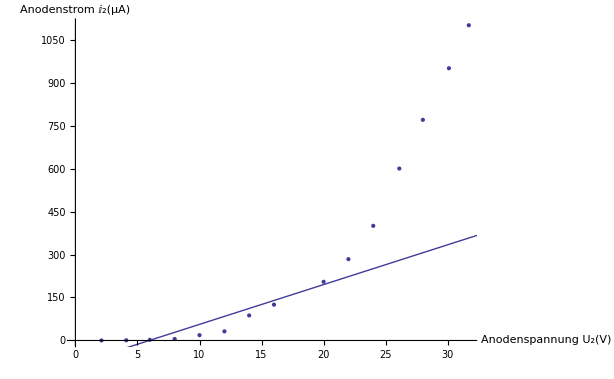

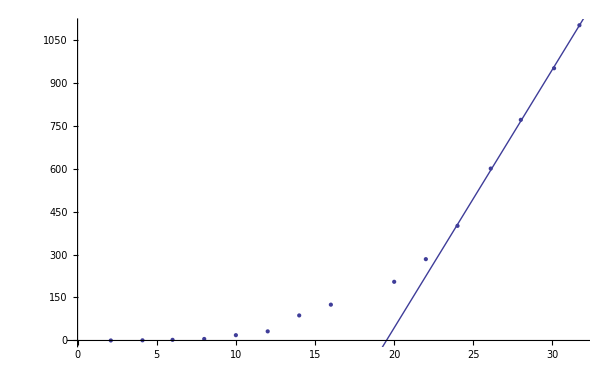

```mathematica
data ={{2.1, 0.04},{4.1, 0.6},{6, 2.26}, {8, 5.29}, {10, 18.53},{12.01, 31.81}, {14, 87.4}, {16, 125},{20, 204.8}, {22, 283.8}, {24, 400}, {26.1, 600}, {28, 770},{30.1, 950}, {31.7, 1100}};
data1 ={{2.1, 0.04},{4.1, 0.6},{6, 2.26}, {8, 5.29}, {10, 18.53},{12.01, 31.81}, {14, 87.4}, {16, 125},{20, 204.8}, {22, 283.8}};
data2 ={{24, 400}, {26.1, 600}, {28, 770},{30.1, 950}, {31.7, 1100}}
dplot = ListPlot[data];
dplot2 = ListPlot[data];
model = LinearModelFit[data1, x, x]
model2 = LinearModelFit[data2, x, x]
Show[dplot, Plot[model["BestFit"],{x, 0, 33}],AxesLabel->{Anodenspannung Subscript[U,2][V],Anodenstrom Subscript[I,2][μA]}]
Show[dplot2, Plot[model2["BestFit"],{x, 0, 33}],AxesLabel->{Anodenspannung Subscript[U,2][V],Anodenstrom Subscript[I,2][μA]}]
```